```mathematica
rect[color_,size_]:=Graphics[{color,Rectangle[{-size,-size},{size,size},RoundingRadius->.4 size]},PlotRange->1,ImageSize->10];
```

```mathematica
rect[RGBColor[1,#,#],#]&/@Range[0.1,1,0.1]//Row
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
img=Style["R",40,Bold]//Rasterize//Binarize//GaussianFilter[#,2.3]&
```

-Graphics-

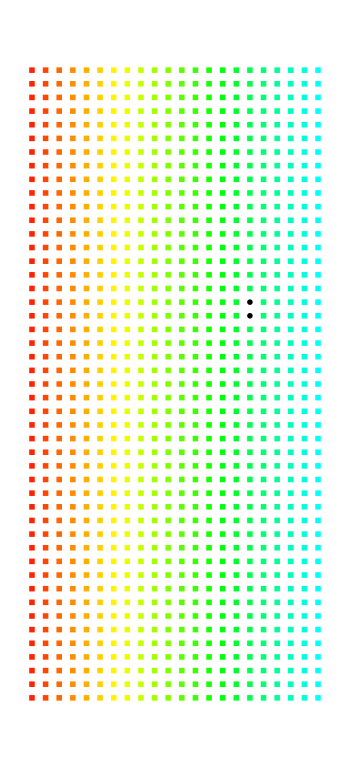

```mathematica
MapIndexed[rect[Hue[#2[[2]]/(2 ImageDimensions[img][[1]])],#1]&,ImageData@img,{2}]//GraphicsGrid[#,ImageSize->350]&
```